Quantum Teleportation |

Synopsispaclet:Q3/tutorial/QuantumTeleportation#255888865 | Implementationpaclet:Q3/tutorial/QuantumTeleportation#1867183189
Simple Theorypaclet:Q3/tutorial/QuantumTeleportation#610843909 | Applicationspaclet:Q3/tutorial/QuantumTeleportation#534588153
Preliminariespaclet:Q3/tutorial/QuantumTeleportation#775468120 |

See also Section 4.1 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Quantum teleportation is a communication protocol that sends quantum information to a distant party by utilizing a pre-shared pair of entangled particles (Bennett et al., 1993). The protocol has attracted public interest since it resembles (fictional) teleportation. In science fiction, (hypothetical) teleportation instantly transports matter or energy across space. Quantum teleportation does not transfer physical objects but only quantum information. Quantum teleportation is also conceptually distinguished from telefax. Telefax makes a copy of the document and sends the duplicated copy while the original document remains at its origin. In quantum teleportation, a quantum state is transferred and disappears from the original system.

Quantum teleportation is one of the first quantum information protocols that vividly illustrates the significance of quantum entanglement as a valuable resource. In this section, we discuss the physical principle behind quantum teleportation and demonstrate the protocol. Another closely related quantum communication protocol is the so-called superdense coding (Bennett and Wiesenr, 1992).

Quantum teleportation is not only interesting in its own right but also used as part of various quantum algorithms. Interestingly, even a computational model based solely on quantum teleportation has been proposed as well (Gottesman and Chuang, 1999; Nielsen, 2003; Leung, 2004).

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol | Circuit representation of elementary gates.
CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | Two-qubit controlled-NOT gate.
Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol | The Hadamard gate.
BellStatepaclet:Q3/ref/BellStateQ3 Package Symbol | Returns a list of the four Bell states.
Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol | Converts QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol and operator (or Ket) expressions to the matrix representation in the standard basis.
ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol | Converts the matrix representation to the corresponding operator or state-vector expression.

Functions related to the quantum teleportation protocol.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Synopsis

Suppose that Bob wants to send one bit of quantum information, say, ψ_C=0_C c_0+1_C c_1 stored in Charlie’s qubit, to Alice residing in a place far away from Bob (and Charlie). There is no quantum communication channel operating between Alice and Bob to directly send the quantum state ψ through. 	Fortunately, however, there is a classical commutation channel.

It is important to note that the quantum state ψ is unknown. The no-cloning theorem prevents a naive approach such as copying and transmitting the quantum state.

## Simple Theory

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

To teleport a quantum state, Alice and Bob need to share an entangled pair of qubits in advance. Suppose that the shared pair of qubits is in the state β_0_(A B), which is one of the four Bell states,

β_0:=(00+11)/(√2),    β_1:=(01+10)/(√2),    β_3:=(01-10)/(√2),    β_3:=(00-11)/(√2).

```mathematica
bs=BellState[S@{1,2}]
```

{(0_S_10_S_2+1_S_11_S_2)/(√2),(0_S_11_S_2+1_S_10_S_2)/(√2),(0_S_11_S_2-1_S_10_S_2)/(√2),(0_S_10_S_2-1_S_11_S_2)/(√2)}

Then, with the quantum state stored in qubit C, that is,

ψ_C=0_C c_0+1_C c_1 ,

```mathematica
msg=Ket[S[3]->0]*c[0]+Ket[S[3]->1]*c[1]
```

c_0 0_S_3+c_1 1_S_3

the initial state Ψ of the overall three qubits at the beginning of the procedure is given by

Ψ=β_0_(A B)⊗ψ_C=(000 c_0+110 c_0+001 c_1+111 c_1)/(√2).

```mathematica
in=bs[[1]]**msg
```

(c_0 0_S_10_S_20_S_3)/(√2)+(c_1 0_S_10_S_21_S_3)/(√2)+(c_0 1_S_11_S_20_S_3)/(√2)+(c_1 1_S_11_S_21_S_3)/(√2)

Recall that Bob has qubits B and C at his hands.

```mathematica
ProductForm[in,{S@1,S@{2,3}}]
```

(c_0 0⊗00)/(√2)+(c_1 0⊗01)/(√2)+(c_0 1⊗10)/(√2)+(c_1 1⊗11)/(√2)

Rewriting the parts consisting of qubits B and C in the Bell basis, the basis consisting of the four Bell states, leads to

Ψ=1/2(0 c_0+1 c_1)_A⊗β_0_(B C)+1/2(0 c_1+1 c_0)_A⊗β_1_(B C)+1/2(0 c_1-1 c_0)_A⊗β_2_(B C)+1/2(0 c_0-1 c_1)_A⊗β_3_(B C)

```mathematica
prj=Dyad[#,#,S@{2,3}]&/@BellState[S@{2,3}];
cmp=prj**in;
cmp//KetFactor//TableForm
```

((c_0 0_S_1+c_1 1_S_1)⊗(0_S_20_S_3+1_S_21_S_3))/(2 √2)
((c_1 0_S_1+c_0 1_S_1)⊗(0_S_21_S_3+1_S_20_S_3))/(2 √2)
-((c_1 0_S_1-c_0 1_S_1)⊗(-0_S_21_S_3+1_S_20_S_3))/(2 √2)
((c_0 0_S_1-c_1 1_S_1)⊗(0_S_20_S_3-1_S_21_S_3))/(2 √2)

The crucial point here is that the state of A in the first term is identical to the original quantum state ψ, and those in the rest are also closely related to ψ by the Pauli operators. More explicitly, one can rewrite the total state vector as

Ψ=ψ_A⊗β_0_(B C)+(Xψ)_A⊗β_1_(B C)+(ⅈ Yψ)_A⊗β_2_(B C)+(Zψ)_A⊗β_3_(B C).

```mathematica
out={1, S[1,1],I*S[1,2],S[1,3]}**cmp;
KetFactor[out]//TableForm
```

((c_0 0_S_1+c_1 1_S_1)⊗(0_S_20_S_3+1_S_21_S_3))/(2 √2)
((c_0 0_S_1+c_1 1_S_1)⊗(0_S_21_S_3+1_S_20_S_3))/(2 √2)
((c_0 0_S_1+c_1 1_S_1)⊗(-0_S_21_S_3+1_S_20_S_3))/(2 √2)
((c_0 0_S_1+c_1 1_S_1)⊗(0_S_20_S_3-1_S_21_S_3))/(2 √2)

Now Bob performs a measurement on the two qubits B and C, owned by Bob, in the Bell basis. The measurement will yield outcomes μ=0,1,2,3 and will collapse the total state vector into the corresponding term, (S^μ ψ)_A⊗β_μ_(B C), where S^0=I, S^1=X, S^2=ⅈ Y, and S^3=Z. The remaining task is for Bob to inform Alice of the outcome μ so that Alice recover the desired state ψ by operating the inverse operator S^μ on her qubit. The information regarding the measurement outcome amounts to two bits, and it requires only a classical channel for transmission.

In short, the quantum teleportation protocol consists of the following steps:

Alice and Bob generate an entangled pair of qubits, A and B, and share the pair between them. This can be done anytime before the procedure actually starts. Bob prepares a quantum state to send in a separate qubit C.

Bob makes a Bell measurement, i.e., the measurement in the Bell basis, on his two qubits B and C.

Bob sends the two-bit information regarding the measurement outcome to Alice through a classical communication channel.

Alice operates a proper inverse operator to recover the desired quantum state.

## Preliminaries

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

In the quantum teleportation protocol, two essential parts are sharing entanglement and performing the Bell measurement. Before we demonstrate an implementation of the quantum teleportation protocol, here we summarize quantum circuit models of the two tasks.

### Entangler Quantum Circuit

To establish an entanglement between two qubits initially in a product state, one needs to interact them. In the quantum circuit model, the interaction is achieve by the CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol gate. Specifically, one can use the feature of the CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol gate that copies the computational basis states of the control qubit to the target qubit,

(0 c_0+1 c_1)⊗0=00 c_0+10 c_1↦00 c_0+11 c_1.

The linear superposition of the control qubit may be built by the Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol gate (a general form of linear superposition can be built with rotation gates).

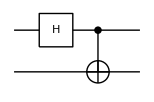

```mathematica
qc=QuantumCircuit[S[1,6],CNOT[S[1],S[2]]]
```

Get the four Bell states applying the above quantum circuit to the product basis.

```mathematica
in=Basis[S@{1,2}];
out=qc**in;
Thread[in->out]//TableForm
```

0_S_10_S_2→(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)
0_S_11_S_2→(0_S_11_S_2)/(√2)+(1_S_10_S_2)/(√2)
1_S_10_S_2→(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2)
1_S_11_S_2→(0_S_11_S_2)/(√2)-(1_S_10_S_2)/(√2)

### Bell-Measurement Circuit

In quantum computers, a measurement usually means to measure the Pauli Z operator on different qubits. In other words, measurement is assumed to be performed independently on individual qubits in the computational basis, {x : x = 0, 1, . . . , 2n − 1}. (In Q3, measurement of arbitrary Pauli operators is supported; see the document of Measurement.)

To measure an arbitrary observable M, one needs to change the basis so that the eigenstates of M are mapped to the computational basis. Specifically, for the Bell measurement (a measurement in the basis of Bell states), the required basis change is equivalent to the inverse procedure of building an entanglement as discussed above. Therefore, the quantum circuit for the Bell measurement may be achieved simply by reversing the order of gates in the entangler circuit.

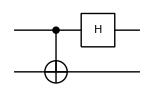

```mathematica
qc=QuantumCircuit[CNOT[S[1],S[2]],S[1,6]]
```

```mathematica
in=BellState[S@{1,2}];
out=qc**in;
Thread[in->out]//TableForm
```

(0_S_10_S_2+1_S_11_S_2)/(√2)→0_S_10_S_2
(0_S_11_S_2+1_S_10_S_2)/(√2)→0_S_11_S_2
(0_S_11_S_2-1_S_10_S_2)/(√2)→1_S_11_S_2
(0_S_10_S_2-1_S_11_S_2)/(√2)→1_S_10_S_2

We note that measurement outcomes (0,0), (0,1), (1,1), and (1,0) corresponds to the Bell states β_0,β_1,β_2, and β_3, respectively.

## Implementation

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Step 1. Alice and Bob generate and share an entangled pair using the quantum entangler circuit discussed above.

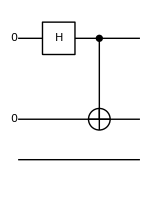

```mathematica
qc1a=QuantumCircuit[Ket[S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Invisible"->S[1.5],"Visible"->S[3]];
Panel[qc1a]
```

Bob also prepares the quantum state to send to Allice and stores it  in Charlie’s qubit C.

```mathematica
msg=Ket[S[3]->0]*c[0]+Ket[S[3]->1]*c[1]
```

c_0 0_S_3+c_1 1_S_3

This is the quantum circuit that fulfills the tasks so far.

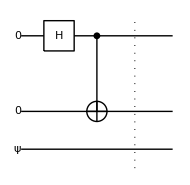

```mathematica
qc1=QuantumCircuit[{msg,"Label"->Ket[ψ]},qc1a,"Separator"]
```

The overall state at this stage is as follows.

```mathematica
out1=Elaborate[qc1]
out1//KetFactor
```

(c_0 0_S_10_S_20_S_3)/(√2)+(c_1 0_S_10_S_21_S_3)/(√2)+(c_0 1_S_11_S_20_S_3)/(√2)+(c_1 1_S_11_S_21_S_3)/(√2)

((0_S_10_S_2+1_S_11_S_2)⊗(c_0 0_S_3+c_1 1_S_3))/(√2)

Step 2. Bob performs a Bell measurement on his qubits. This can be done by reversing the entangler circuit as explained in the above.

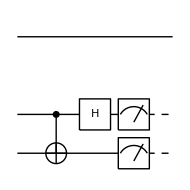

(0_S_20_S_3+1_S_21_S_3)/(√2)→0_S_20_S_3
(0_S_21_S_3+1_S_20_S_3)/(√2)→0_S_21_S_3
(0_S_21_S_3-1_S_20_S_3)/(√2)→1_S_21_S_3
(0_S_20_S_3-1_S_21_S_3)/(√2)→1_S_20_S_3

```mathematica
qc2a=QuantumCircuit[
CNOT[S[2],S[3]],S[2,6],
Measurement[S[{2,3},3]],
"Visible"->S[1],"Invisible"->S[1.5]];
Panel[qc2a]
bs=BellState[S@{2,3}];
ls=qc2a**bs;
Transpose@Thread[bs->ls]//TableForm
```

The overall quantum circuit so far is as follows.

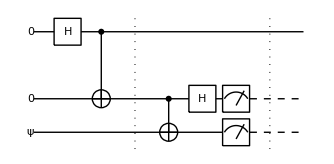

```mathematica
qc2=QuantumCircuit[qc1,qc2a,"Separator"]
```

This is the state of the total system expected at this stage.

```mathematica
normalizationRules={c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1};
out2=ExpressionFor[qc2]/.normalizationRules;
out2//KetFactor
```

1/2 (c_1 0_S_1+c_0 1_S_1)⊗0_S_21_S_3

Step 3. Bob sends the measurement outcome to Alice through a classical channel.
Step 4. Alice applies a proper unitary gate on her qubit in accordance with Bob’s message. These two steps are simulated by a feedback control.

Combining all the steps, one can transmit a quantum state to a remote party without a quantum channel.

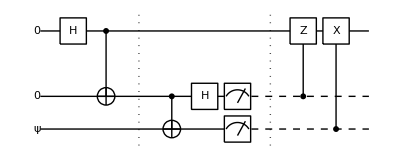

```mathematica
qc=QuantumCircuit[qc2,ControlledGate[S[2],S[1,3]],ControlledGate[S[3],S[1,1]],"Invisible"->S[1.5]]
```

This is the final state of the total system.

```mathematica
out=ExpressionFor[qc]/.normalizationRules;
out//KetFactor
```

1/2 (c_0 0_S_1+c_1 1_S_1)⊗0_S_21_S_3

Note that the Bell measurement outcomes are uniformed distributed, and the state resulting in Alice’s qubit is always the same as the original quantum state (msg) regardless of the measurement outcome.

```mathematica
EchoTiming[
data=Table[ExpressionFor[qc]/.normalizationRules;Readout[S[{2,3},3]],300];]
Histogram3D[data,Ticks->{{0,1},{0,1},Automatic},AxesLabel->{"Z_2","Z_3","Counts"}]
```

7.97472

-Graphics3D-

## Applications

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

As mentioned at the beginning, quantum teleportation is not only interesting in its own right but also used as part of various quantum algorithms. In fact, universal quantum computation based solely on quantum teleportation is possible (Gottesman and Chuang, 1999; Nielsen, 2003; Leung, 2004). For photonic quantum computers, this is vital because photons do not interact with each other and hence the CNOT gate is impossible with usual linear optics (Knill, Laflamme, and Milburn, 2001).

The CNOT gate can be achieved using the quantum teleportation (Gottesman and Chuang, 1999). The quantum circuit in Figure 1 summarizes the procedure. Below, we analyse the quantum circuit in detail.

-Graphics-

Figure 1: A quantum circuit to realize the CNOT gate using quantum teleportation. The first and last qubits are the control and target qubits, respectively, and the result is stored in the third and forth qubits, respectively. Here, the two Bell measurements (between the vertical dashed lines) are implemented through the usual gate operations and measurements in the computational basis. In realistic situations, however, they are achieved (non-deterministically in many cases) using special measurement devices (such as parity measurement).

First, generate the entanglement in the ancillary quantum register.

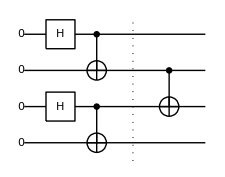

```mathematica
entangler=QuantumCircuit[
Ket[S@{2,3,4,5}],
S[{2,4},6],{CNOT[S[2],S[3]],CNOT[S[4],S[5]]},
"Separator",
CNOT[S[3],S[4]]
]
```

```mathematica
chi=Elaborate[entangler];
KetFactor[chi,S@{2,3}]
```

0_S_20_S_3⊗(1/2 0_S_40_S_5+1/2 1_S_41_S_5)+1_S_21_S_3⊗(1/2 0_S_41_S_5+1/2 1_S_40_S_5)

Here is the core part of the quantum circuit to implement the CNOT gate using quantum teleportation.

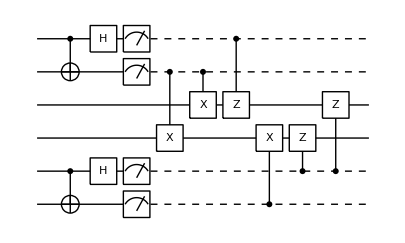

```mathematica
core=QuantumCircuit[
{CNOT[S[1],S[2]],CNOT[S[5],S[6]]},
S[{1,5},6],Measurement[S[{1,2,5,6},3]],
ControlledGate[S[2],S[4,1]],ControlledGate[S[2],S[3,1]],
ControlledGate[S[1],S[3,3]],
ControlledGate[S[6],S[4,1]],
ControlledGate[S[5],S[4,3]],ControlledGate[S[5],S[3,3]]
]
```

Let us construct a small subroutine to facilitate the test of the above quantum circuit.

```mathematica
qtCNOT[{x_,y_}]:=Block[
{in=Ket[S[1]->x,S[6]->y]},
qc=QuantumCircuit[in,
{chi,"Label"->Ket["χ"]},
core
];
Echo[qc];
Table[KetRegulate[KetDrop[Elaborate[qc],S@{1,2,5,6}],S@{3,4}],20]
]
```

```mathematica
qtCNOT[{0,0}]
```

-Graphics-

-Graphics-

```mathematica
qtCNOT[{0,1}]
```

-Graphics-

-Graphics-

```mathematica
qtCNOT[{1,0}]
```

-Graphics-

-Graphics-

```mathematica
qtCNOT[{1,1}]
```

-Graphics-

-Graphics-

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Algorithms
▪QuantumCircuit Usage Examples
▪Quantum Information Systems with Q3

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/

| Related Links
▪C. H. Bennet, G. Brassard, C. Crepeau, R. Jozsa, A. Peres, and W. K. Wootters, Physical Review Letters 70, 1895 (1993)https://doi.org/10.1103/PhysRevLett.70.1895, “Teleporting an Unknown Quantum State via Dual Classical and Einstein-Podolsky-Rosen Channels.”
▪C. H. Bennett and S. J. Wiesner, Physical Review Letters 69 (20), 2881 (1992)https://doi.org/10.1103/PhysRevLett.69.2881, “Communication via one- and two-particle operators on Einstein-Podolsky-Rosen states.”
▪D. Gottesman and I. Chuang, Nature 402, 390-393 (1999)https://doi.org/10.1038/46503, "Quantum teleportation as a universal computational primitive."
▪M. A. Nielsen. Physics Letters A, 308, 96–100 (2003)https://doi.org/10.1016/S0375-9601(02)01803-0, “Quantum computation by measurement and quantum memory.”
▪D. W. Leung, International Journal of Quantum Information 2, 33-43, (2004)https://doi.org/10.1142/S0219749904000055, “Quantum computation by measurements.”
▪E. Knill, R. Laflamme, and G. J. Bilburn, Nature 409, 46 (2001)https://doi.org/10.1038/35051009, "A scheme for efficient quantum computation with linear optics."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).